## Working out the model of known components

### These known components come from fig. 4 of 2104.03315

```mathematica
AppendTo[$Path, "/Users/matias/Downloads/blazar_data/"];
logSpace[start_,end_,num_]:=10^(Range[Log10[start],Log10[end],(Log10[end]-Log10[start])/(num-1)])
```

```mathematica
SFlowerArr=Import["known_components/SF_lower.csv","CSV"];
SFmidArr=Import["known_components/SF_mid.csv","CSV"];
SFupperArr=Import["known_components/SF_upper.csv","CSV"];
mAGNlowerArr=Import["known_components/mAGN_lower.csv","CSV"];
mAGNmidArr=Import["known_components/mAGN_mid.csv","CSV"];
mAGNupperArr=Import["known_components/mAGN_upper.csv","CSV"];
FSRQlowerArr=Import["known_components/fsrq_lower.csv","CSV"];
FSRQmidArr=Import["known_components/fsrq_mid.csv","CSV"];
FSRQupperArr=Import["known_components/fsrq_upper.csv","CSV"];
LAClowerArr=Import["known_components/bllac_lower.csv","CSV"];
LACmidArr=Import["known_components/bllac_mid.csv","CSV"];
LACupperArr=Import["known_components/bllac_upper.csv","CSV"];
knownMidArr=Import["known_components/all_mid.csv","CSV"];
knownUpperArr=Import["known_components/all_upper.csv","CSV"];
knownLowerArr=Import["known_components/all_lower.csv","CSV"];
```

```mathematica
SFlowerInterp=Interpolation[SFlowerArr];
SFmidInterp=Interpolation[SFmidArr];
SFupperInterp=Interpolation[SFupperArr];
mAGNlowerInterp=Interpolation[mAGNlowerArr];
mAGNmidInterp=Interpolation[mAGNmidArr];
mAGNupperInterp=Interpolation[mAGNupperArr];
FSRQlowerInterp=Interpolation[FSRQlowerArr];
FSRQmidInterp=Interpolation[FSRQmidArr];
FSRQupperInterp=Interpolation[FSRQupperArr];
LAClowerInterp=Interpolation[LAClowerArr];
LACmidInterp=Interpolation[LACmidArr];
LACupperInterp=Interpolation[LACupperArr];
knownMidInterp=Interpolation[knownMidArr];
knownUpperInterp=Interpolation[knownUpperArr];
knownLowerInterp=Interpolation[knownLowerArr];
```

```mathematica
SFlower[x_]:=Piecewise[{
{SFlowerInterp[x],x<=Max[SFlowerArr[[All,1]]]},
{0,x>Max[SFlowerArr[[All,1]]]}
}];
SFmid[x_]:=Piecewise[{
{SFmidInterp[x],x<=Max[SFmidArr[[All,1]]]},
{0,x>Max[SFmidArr[[All,1]]]}
}];
SFupper[x_]:=Piecewise[{
{SFupperInterp[x],x<=Max[SFupperArr[[All,1]]]},
{0,x>Max[SFupperArr[[All,1]]]}
}];
mAGNlower[x_]:=Piecewise[{
{mAGNlowerInterp[x],x<=Max[mAGNlowerArr[[All,1]]]},
{0,x>Max[mAGNlowerArr[[All,1]]]}
}];
mAGNmid[x_]:=Piecewise[{
{mAGNmidInterp[x],x<=Max[mAGNmidArr[[All,1]]]},
{0,x>Max[mAGNmidArr[[All,1]]]}
}];
mAGNupper[x_]:=Piecewise[{
{mAGNupperInterp[x],x<=Max[mAGNupperArr[[All,1]]]},
{0,x>Max[mAGNupperArr[[All,1]]]}
}];
FSRQlower[x_]:=Piecewise[{
{FSRQlowerInterp[x],x<=Max[FSRQlowerArr[[All,1]]]},
{0,x>Max[FSRQlowerArr[[All,1]]]}
}];
FSRQmid[x_]:=Piecewise[{
{FSRQmidInterp[x],x<=Max[FSRQmidArr[[All,1]]]},
{0,x>Max[FSRQmidArr[[All,1]]]}
}];
FSRQupper[x_]:=Piecewise[{
{FSRQupperInterp[x],x<=Max[FSRQupperArr[[All,1]]]},
{0,x>Max[FSRQupperArr[[All,1]]]}
}];
LAClower[x_]:=Piecewise[{
{LAClowerInterp[x],x<=Max[LAClowerArr[[All,1]]]},
{0,x>Max[LAClowerArr[[All,1]]]}
}];
LACmid[x_]:=Piecewise[{
{LACmidInterp[x],x<=Max[LACmidArr[[All,1]]]},
{0,x>Max[LACmidArr[[All,1]]]}
}];
LACupper[x_]:=Piecewise[{
{LACupperInterp[x],x<=Max[LACupperArr[[All,1]]]},
{0,x>Max[LACupperArr[[All,1]]]}
}];
knownMid[x_]:=Piecewise[{
{knownMidInterp[x],x<=Max[knownMidArr[[All,1]]]},
{0,x>Max[knownMidArr[[All,1]]]}
}];
knownUpper[x_]:=Piecewise[{
{knownUpperInterp[x],x<=Max[knownUpperArr[[All,1]]]},
{0,x>Max[knownUpperArr[[All,1]]]}
}];
knownLower[x_]:=Piecewise[{
{knownLowerInterp[x],x<=Max[knownLowerArr[[All,1]]]},
{0,x>Max[knownLowerArr[[All,1]]]}
}];
```

```mathematica
arr=logSpace[0.2,700,1000];
SFmidData=Table[{i,SFmid[i]},{i,arr}];
SFlowerData=Table[{i,SFlower[i]},{i,arr}];
SFupperData=Table[{i,SFupper[i]},{i,arr}];
mAGNmidData=Table[{i,mAGNmid[i]},{i,arr}];
mAGNlowerData=Table[{i,mAGNlower[i]},{i,arr}];
mAGNupperData=Table[{i,mAGNupper[i]},{i,arr}];
FSRQlowerData=Table[{i,FSRQlower[i]},{i,arr}];
FSRQmidData=Table[{i,FSRQmid[i]},{i,arr}];
FSRQupperData=Table[{i,FSRQupper[i]},{i,arr}];
LACmidData=Table[{i,LACmid[i]},{i,arr}];
LAClowerData=Table[{i,LAClower[i]},{i,arr}];
LACupperData=Table[{i,LACupper[i]},{i,arr}];
knownMidData=Table[{i,knownMid[i]},{i,arr}];
knownLowerData=Table[{i,knownLower[i]},{i,arr}];
knownUpperData=Table[{i,knownUpper[i]},{i,arr}];
```

```mathematica
SFerrorUpper=SFupperData[[All,2]]/SFmidData[[All,2]]-1;
SFerrorLower=1-SFlowerData[[All,2]]/SFmidData[[All,2]];
mAGNerrorUpper=mAGNupperData[[All,2]]/mAGNmidData[[All,2]]-1;
mAGNerrorLower=1-mAGNlowerData[[All,2]]/mAGNmidData[[All,2]];
FSRQerrorUpper=FSRQupperData[[All,2]]/FSRQmidData[[All,2]]-1/. Indeterminate->0/.ComplexInfinity->0//Quiet;
FSRQerrorLower=1-FSRQlowerData[[All,2]]/FSRQmidData[[All,2]]/. Indeterminate->0/.ComplexInfinity->0//Quiet;
LACerrorUpper=LACupperData[[All,2]]/LACmidData[[All,2]]-1/. Indeterminate->0/.ComplexInfinity->0//Quiet;
LACerrorLower=1-LAClowerData[[All,2]]/LACmidData[[All,2]]/. Indeterminate->0/.ComplexInfinity->0//Quiet;
```

```mathematica
SFmidLog=Log10@SFmidData;
SFupperLog=Log10@SFupperData;
SFlowerLog=Log10@SFlowerData;
mAGNmidLog=Log10@mAGNmidData;
mAGNupperLog=Log10@mAGNupperData;
mAGNlowerLog=Log10@mAGNlowerData;
FSRQupperLog=Log10@FSRQupperData;
FSRQlowerLog=Log10@FSRQlowerData;
FSRQmidLog=Log10@FSRQmidData;
LACupperLog=Log10@LACupperData;
LAClowerLog=Log10@LAClowerData;
LACmidLog=Log10@LACmidData;
knownMidLog=Log10@knownMidData;
```

```mathematica
SFdzUpper=(1/Log[10])*SFerrorUpper;
SFdzLower=(1/Log[10])*SFerrorLower;
mAGNdzUpper=(1/Log[10])*mAGNerrorUpper;
mAGNdzLower=(1/Log[10])*mAGNerrorLower;
FSRQdzUpper=(1/Log[10])*FSRQerrorUpper;
FSRQdzLower=(1/Log[10])*FSRQerrorLower;
LACdzUpper=(1/Log[10])*LACerrorUpper;
LACdzLower=(1/Log[10])*LACerrorLower;
SFdyUpper=SFupperData[[All,2]]*(10^SFdzUpper-1);
SFdyLower=SFlowerData[[All,2]]*(10^SFdzLower-1);
mAGNdyUpper=mAGNupperData*(10^mAGNdzUpper-1);
mAGNdyLower=mAGNlowerData*(10^mAGNdzLower-1);
FSRQdyUpper=FSRQupperData*(10^FSRQdzUpper-1);
FSRQdyLower=FSRQlowerData*(10^FSRQdzLower-1);
LACdyUpper=LACupperData*(10^LACdzUpper-1);
LACdyLower=LAClowerData*(10^LACdzLower-1);
(*combinedUpperError=Sqrt[SFdyUpper^2]*)
(*combinedLowerError=Sqrt[SFdzLower^2+mAGNdzLower^2+FSRQdzLower^2+LACdzLower^2];
combinedUpperError=Sqrt[SFdzUpper^2+mAGNdzUpper^2+FSRQdzUpper^2+LACdzUpper^2];*)
```

```mathematica
ClearAll[mAGNΔy,mAGNΔf]
SFΔy=(SFupperLog[[All,2]]/SFlowerLog[[All,2]])/2;
SFΔf=1/Log[10]*SFΔy;
mAGNΔy=(mAGNupperLog[[All,2]]/mAGNlowerLog[[All,2]])/2;
mAGNΔf=1/Log[10]*mAGNΔy;
FSRQΔy=(FSRQupperLog[[All,2]]/FSRQlowerLog[[All,2]])/2/.Indeterminate->0;
FSRQΔf=1/Log[10]*FSRQΔy;
LACΔy=(LACupperLog[[All,2]]/LAClowerLog[[All,2]])/2/.Indeterminate->0;
LACΔf=1/Log[10]*LACΔy;
totalError=10^Sqrt[SFΔf^2+mAGNΔf^2+FSRQΔf^2+LACΔf^2];
```

Infinity::indet: Indeterminate expression 0 (-∞) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

```mathematica
Dimensions@knownMidArr
```

{102,2}

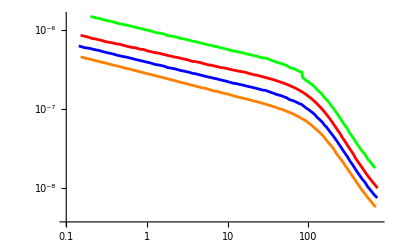

```mathematica
ListLogLogPlot[{knownMidArr,Transpose[{knownMidData[[All,1]],knownMidData[[All,2]]*totalError}],knownUpperArr,knownLowerArr},Joined->True,PlotStyle->{Blue,Green,Red,Orange}]
```

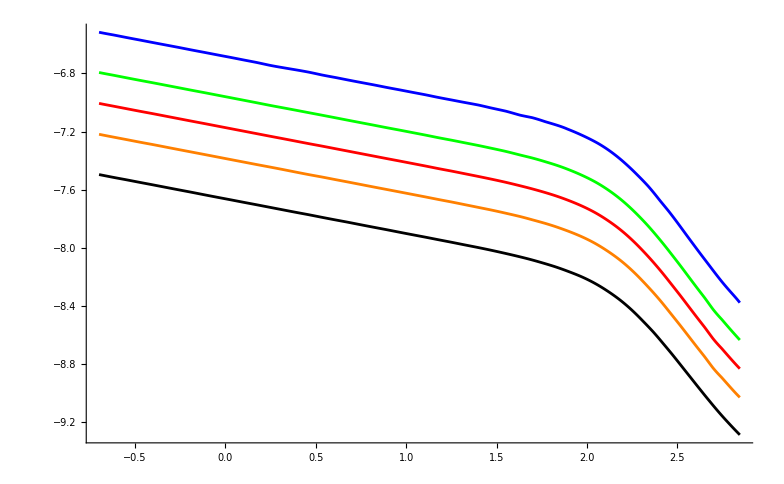

```mathematica
ListPlot[{mAGNmidLog,mAGNupperLog,mAGNlowerLog,Transpose[{mAGNmidLog[[All,1]],mAGNmidLog[[All,2]]+mAGNΔf}],Transpose[{mAGNmidLog[[All,1]],mAGNmidLog[[All,2]]-mAGNΔf}]},Joined->True,PlotStyle->{Red,Blue,Black,Green,Orange}]
```

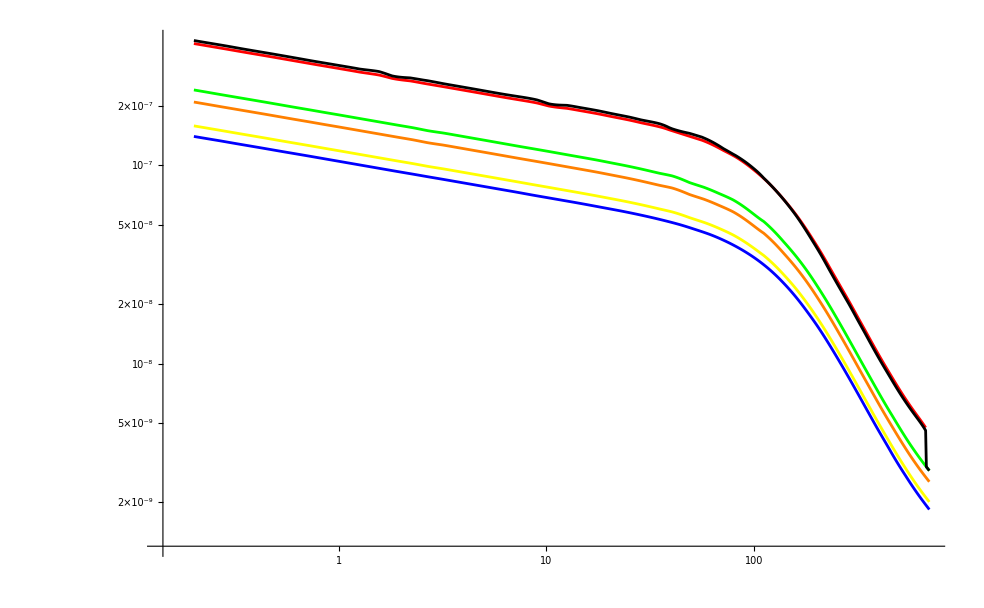

```mathematica
ListLogLogPlot[{SFlowerData,SFmidData,SFupperData,Transpose[{SFmidData[[All,1]],SFmidData[[All,2]]*10^(-SFdzLower)}],Transpose[{SFmidData[[All,1]],SFmidData[[All,2]]+(1/Log[10]*SFdyUpper)}],Transpose[{SFmidData[[All,1]],SFmidData[[All,2]]-(1/Log[10]*SFdyLower)}]},Joined->True,PlotStyle->{Blue,Green,Red,Yellow,Black,Orange}]
```

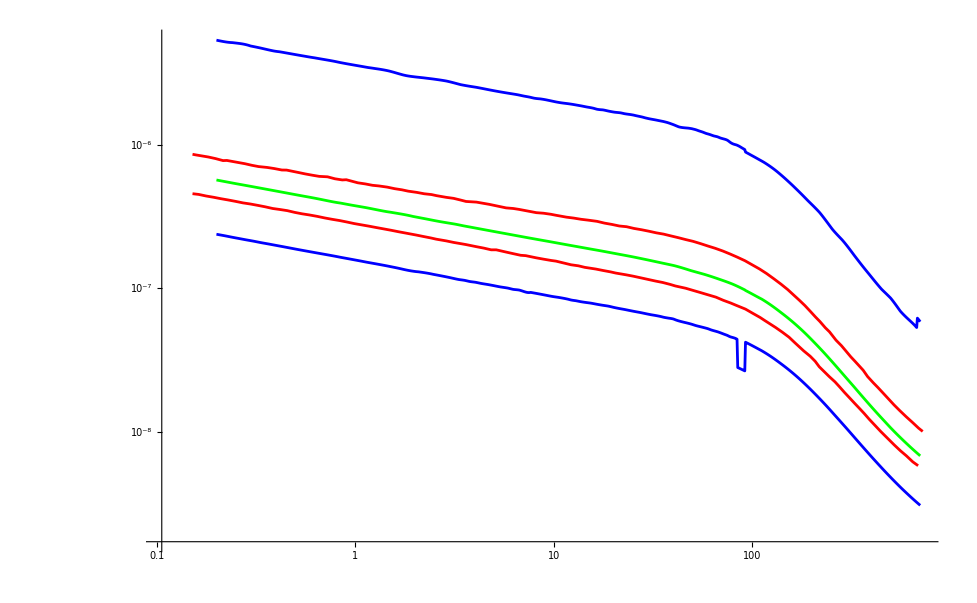

```mathematica
combinedMid=Transpose[{SFmidData[[All,1]],SFmidData[[All,2]]+mAGNmidData[[All,2]]+FSRQmidData[[All,2]]+LACmidData[[All,2]]}];
combinedUpper=Transpose[{combinedMid[[All,1]],combinedMid[[All,2]]*(10^combinedUpperError)}];
combinedLower=Transpose[{combinedMid[[All,1]],combinedMid[[All,2]]*(10^(-combinedLowerError))}];
(*knownLower[x_]:=Piecewise[{{0,x>700},{Evaluate[Interpolation[combinedLower]][x],x<700}}];
knownMid[x_]:=Piecewise[{{0,x>700},{Evaluate[Interpolation[combinedMid]][x],x<700}}];knownUpper[x_]:=Piecewise[{{0,x>700},{Evaluate[Interpolation[combinedUpper]][x],x<700}}];*)
ListLogLogPlot[{knownLower,knownUpper,combinedLower,combinedUpper,combinedMid},Joined->True,PlotStyle->{Red,Red,Blue,Blue,Green}]
```

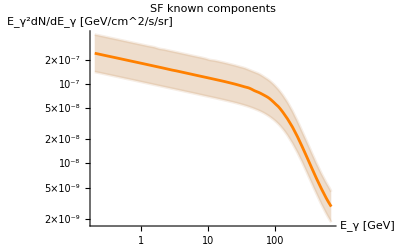

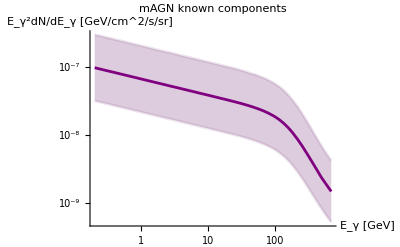

```mathematica
LogLogPlot[{SFmid[x],SFlower[x],SFupper[x]},{x,0.2,700},Filling->{2->{3}},PlotStyle->{{Orange},{Opacity[0.1],Darker@Orange},{Opacity[0.1],Darker@Orange}},PlotLabel->"SF known components",AxesLabel->{"E_γ [GeV]","E_γ^2dN/dE_γ [GeV/cm^2/s/sr]"}]
LogLogPlot[{mAGNmid[x],mAGNlower[x],mAGNupper[x]},{x,0.2,700},Filling->{2->{3}},PlotStyle->{{Purple},{Opacity[0.1],Darker@Purple},{Opacity[0.1],Darker@Purple}},PlotLabel->"mAGN known components",AxesLabel->{"E_γ [GeV]","E_γ^2dN/dE_γ [GeV/cm^2/s/sr]"}]
```

```mathematica
σSF=(SFupperData[[All,2]]/SFlowerData[[All,2]])/2;
σmAGN=(mAGNupperData[[All,2]]/mAGNlowerData[[All,2]])/2;
σFSRQ=(FSRQupperData[[All,2]]/FSRQlowerData[[All,2]])/2/.ComplexInfinity->0/.Indeterminate->0//Quiet;
σLAC=(LACupperData[[All,2]]/LAClowerData[[All,2]])/2/.ComplexInfinity->0/.Indeterminate->0//Quiet;
```

```mathematica
(*σtot=Sqrt[(σSF/SFmidData[[All,2]])^2+(σmAGN/mAGNmidData[[All,2]])^2+(σFSRQ/FSRQmidData[[All,2]])^2+(σLAC/LACmidData[[All,2]])^2]/.Indeterminate->0 //Quiet;*)
σtot=1/(Sqrt[2]*Log[10])*Sqrt[(σSF)^2+(σmAGN)^2+(σFSRQ)^2+(σLAC)^2]/.Indeterminate->0 //Quiet;
```

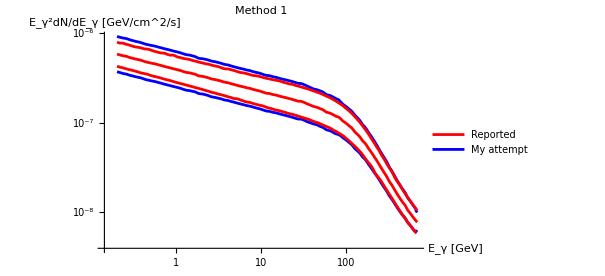

```mathematica
arr=logSpace[0.2,700,1000];
combinedUpper=Table[{arr[[i]],knownMid[arr[[i]]]*σtot[[i]]},{i,Length[arr]}];
combinedLower=Table[{arr[[i]],knownMid[arr[[i]]]/σtot[[i]]},{i,Length[arr]}];
ListLogLogPlot[{knownMidData,combinedUpper,combinedLower,knownUpperData,knownLowerData},Joined->True,PlotStyle->{Red,Blue,Blue,Red,Red},PlotLegends->Placed[{"Reported","My attempt"},{0.5,0.2}],AxesLabel->{"E_γ [GeV]","E_γ^2dN/dE_γ [GeV/cm^2/s]"},PlotLabel->"Method 1"]
```

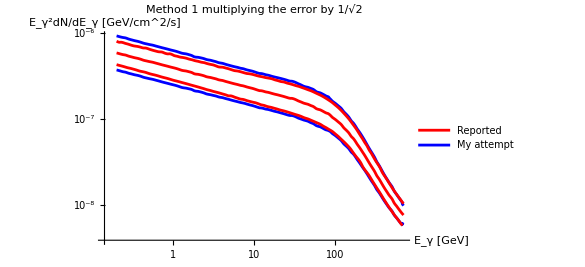

```mathematica
arr=logSpace[0.2,700,1000];
combinedUpper=Table[{arr[[i]],knownMid[arr[[i]]]*σtot[[i]]},{i,Length[arr]}];
combinedLower=Table[{arr[[i]],knownMid[arr[[i]]]/σtot[[i]]},{i,Length[arr]}];
ListLogLogPlot[{knownMidData,combinedUpper,combinedLower,knownUpperData,knownLowerData},Joined->True,PlotStyle->{Red,Blue,Blue,Red,Red},PlotLegends->Placed[{"Reported","My attempt"},{0.5,0.2}],AxesLabel->{"E_γ [GeV]","E_γ^2dN/dE_γ [GeV/cm^2/s]"},PlotLabel->"Method 1 multiplying the error by 1/√2"]
```

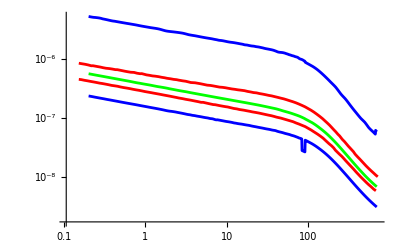

```mathematica
ListLogLogPlot[{knownLower,knownUpper,combinedLower,combinedUpper,combinedMid},Joined->True,PlotStyle->{Red,Red,Blue,Blue,Green}]
```

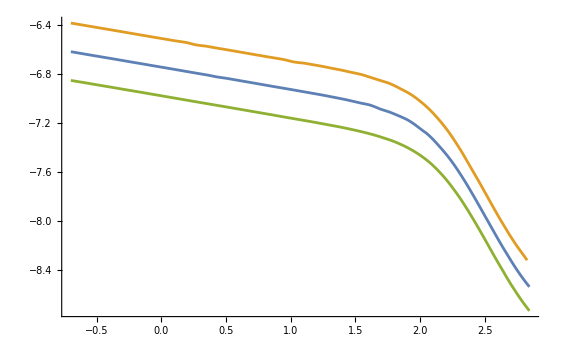

```mathematica
ListPlot[{SFmidLog,SFupperLog,SFlowerLog},Joined->True]
```

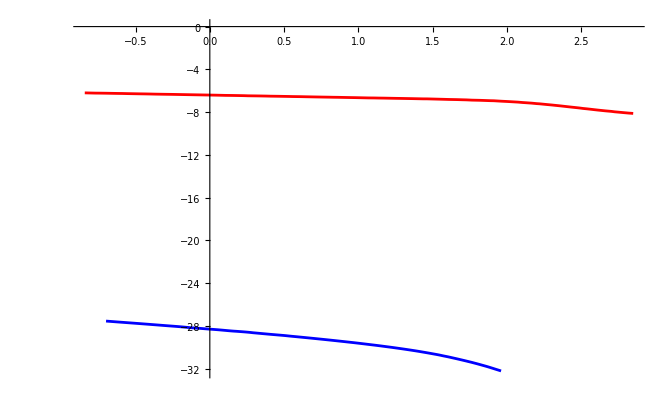

```mathematica
ListPlot[{Log10@knownMidArr,Transpose[{SFmidLog[[All,1]],SFmidLog[[All,2]]+mAGNmidLog[[All,2]]+FSRQmidLog[[All,2]]+LACmidLog[[All,2]]}]},Joined->True,PlotStyle->{Red,Blue},PlotRange->All]
```

```mathematica
SFlogDiff=Transpose[{SFupperLog[[All,1]],(SFupperLog[[All,2]]-SFlowerLog[[All,2]])/2}]/.-Infinity->0//Quiet;
mAGNlogDiff=Transpose[{SFupperLog[[All,1]],(mAGNupperLog[[All,2]]-mAGNlowerLog[[All,2]])/2}];
LAClogDiff=Transpose[{SFupperLog[[All,1]],(LACupperLog[[All,2]]-LAClowerLog[[All,2]])/2}];
FSRQlogDiff=Transpose[{SFupperLog[[All,1]],(FSRQupperLog[[All,2]]-FSRQlowerLog[[All,2]])/2}]/.Infinity->0/.Indeterminate->0//Quiet;
```

```mathematica
allError=Transpose[{SFlogDiff[[All,1]],1/(Log[10])*Sqrt[SFlogDiff[[All,2]]^2+mAGNlogDiff[[All,2]]^2+LAClogDiff[[All,2]]^2+FSRQlogDiff[[All,2]]^2]}];
```

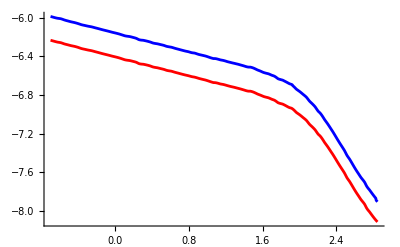

```mathematica
ListPlot[{knownMidLog,Transpose[{allError[[All,1]],knownMidLog[[All,2]]+allError[[All,2]]}]},Joined->True,PlotRange->All,PlotStyle->{Red,Blue}]
```

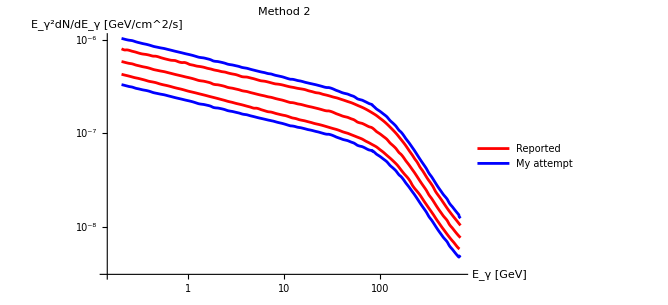

```mathematica
ListLogLogPlot[{knownMidData,Transpose[{10^allError[[All,1]],knownMidData[[All,2]]*10^allError[[All,2]]}],Transpose[{10^allError[[All,1]],knownMidData[[All,2]]/10^allError[[All,2]]}],knownUpperData,knownLowerData},Joined->True,PlotRange->All,PlotStyle->{Red,Blue,Blue,Red,Red},PlotLegends->Placed[{"Reported","My attempt"},{0.5,0.2}],AxesLabel->{"E_γ [GeV]","E_γ^2dN/dE_γ [GeV/cm^2/s]"},PlotLabel->"Method 2"]
```

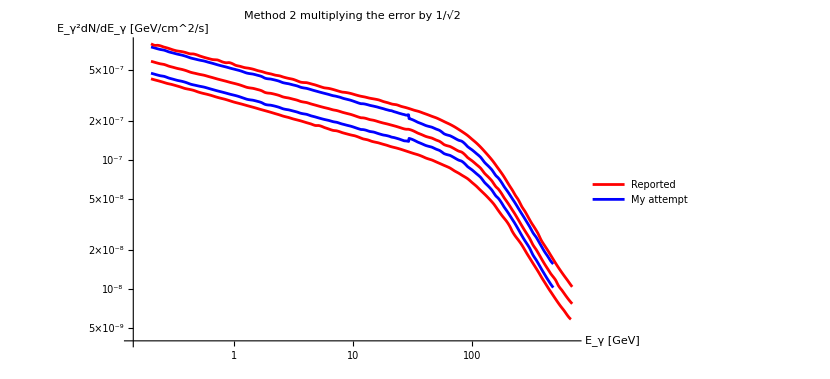

```mathematica
ListLogLogPlot[{knownMidData,Transpose[{10^allError[[All,1]],knownMidData[[All,2]]*10^(1/Sqrt[2*Log@2]*allError[[All,2]])}],Transpose[{10^allError[[All,1]],knownMidData[[All,2]]/10^(1/Sqrt[2]*allError[[All,2]])}],knownUpperData,knownLowerData},Joined->True,PlotRange->All,PlotStyle->{Red,Blue,Blue,Red,Red},PlotLegends->Placed[{"Reported","My attempt"},{0.5,0.2}],AxesLabel->{"E_γ [GeV]","E_γ^2dN/dE_γ [GeV/cm^2/s]"},PlotLabel->"Method 2 multiplying the error by 1/√2"]
```

### Couldn’t get above one to work, so trying to recreate fig. 1 of 1811.05988

```mathematica
SFlowerArr=Import["known_test/SF_lower.csv","CSV"];
SFupperArr=Import["known_test/SF_upper.csv","CSV"];
mAGNlowerArr=Import["known_test/mAGN_lower.csv","CSV"];
mAGNupperArr=Import["known_test/mAGN_upper.csv","CSV"];
FSRQlowerArr=Import["known_test/FSRQ_lower.csv","CSV"];
FSRQupperArr=Import["known_test/FSRQ_upper.csv","CSV"];
LAClowerArr=Import["known_test/LAC_lower.csv","CSV"];
LACupperArr=Import["known_test/LAC_upper.csv","CSV"];
knownMidArr=Import["known_test/all_mid.csv","CSV"];
knownUpperArr=Import["known_test/all_upper.csv","CSV"];
knownLowerArr=Import["known_test/all_lower.csv","CSV"];
```

```mathematica
SFlowerInterp=Interpolation[SFlowerArr];
SFupperInterp=Interpolation[SFupperArr];
mAGNlowerInterp=Interpolation[mAGNlowerArr];
mAGNupperInterp=Interpolation[mAGNupperArr];
FSRQlowerInterp=Interpolation[FSRQlowerArr];
FSRQupperInterp=Interpolation[FSRQupperArr];
LAClowerInterp=Interpolation[LAClowerArr];
LACupperInterp=Interpolation[LACupperArr];
knownMidInterp=Interpolation[knownMidArr];
knownUpperInterp=Interpolation[knownUpperArr];
knownLowerInterp=Interpolation[knownLowerArr];
```

```mathematica
SFlower[x_]:=Piecewise[{
{SFlowerInterp[x],x<=Max[SFlowerArr[[All,1]]]},
{0,x>Max[SFlowerArr[[All,1]]]}
}];
SFupper[x_]:=Piecewise[{
{SFupperInterp[x],x<=Max[SFupperArr[[All,1]]]},
{0,x>Max[SFupperArr[[All,1]]]}
}];
mAGNlower[x_]:=Piecewise[{
{mAGNlowerInterp[x],x<=Max[mAGNlowerArr[[All,1]]]},
{0,x>Max[mAGNlowerArr[[All,1]]]}
}];
mAGNupper[x_]:=Piecewise[{
{mAGNupperInterp[x],x<=Max[mAGNupperArr[[All,1]]]},
{0,x>Max[mAGNupperArr[[All,1]]]}
}];
FSRQlower[x_]:=Piecewise[{
{FSRQlowerInterp[x],x<=Max[FSRQlowerArr[[All,1]]]},
{0,x>Max[FSRQlowerArr[[All,1]]]}
}];
FSRQupper[x_]:=Piecewise[{
{FSRQupperInterp[x],x<=Max[FSRQupperArr[[All,1]]]},
{0,x>Max[FSRQupperArr[[All,1]]]}
}];
LAClower[x_]:=Piecewise[{
{LAClowerInterp[x],x<=Max[LAClowerArr[[All,1]]]},
{0,x>Max[LAClowerArr[[All,1]]]}
}];
LACupper[x_]:=Piecewise[{
{LACupperInterp[x],x<=Max[LACupperArr[[All,1]]]},
{0,x>Max[LACupperArr[[All,1]]]}
}];
knownMid[x_]:=Piecewise[{
{knownMidInterp[x],x<=Max[knownMidArr[[All,1]]]},
{0,x>Max[knownMidArr[[All,1]]]}
}];
knownUpper[x_]:=Piecewise[{
{knownUpperInterp[x],x<=Max[knownUpperArr[[All,1]]]},
{0,x>Max[knownUpperArr[[All,1]]]}
}];
knownLower[x_]:=Piecewise[{
{knownLowerInterp[x],x<=Max[knownLowerArr[[All,1]]]},
{0,x>Max[knownLowerArr[[All,1]]]}
}];
```

```mathematica
arr=logSpace[0.2,700,1000];
SFlowerData=Table[{i,SFlower[i]},{i,arr}];
SFupperData=Table[{i,SFupper[i]},{i,arr}];
mAGNlowerData=Table[{i,mAGNlower[i]},{i,arr}];
mAGNupperData=Table[{i,mAGNupper[i]},{i,arr}];
FSRQlowerData=Table[{i,FSRQlower[i]},{i,arr}];
FSRQupperData=Table[{i,FSRQupper[i]},{i,arr}];
LAClowerData=Table[{i,LAClower[i]},{i,arr}];
LACupperData=Table[{i,LACupper[i]},{i,arr}];
knownMidData=Table[{i,knownMid[i]},{i,arr}];
knownUpperData=Table[{i,knownUpper[i]},{i,arr}];
knownLowerData=Table[{i,knownLower[i]},{i,arr}];
```

```mathematica
SFupperLog=Log10@SFupperData;
SFlowerLog=Log10@SFlowerData;
mAGNupperLog=Log10@mAGNupperData;
mAGNlowerLog=Log10@mAGNlowerData;
FSRQupperLog=Log10@FSRQupperData;
FSRQlowerLog=Log10@FSRQlowerData;
LACupperLog=Log10@LACupperData;
LAClowerLog=Log10@LAClowerData;
```

```mathematica
SFlogDiff=Transpose[{SFupperLog[[All,1]],(SFupperLog[[All,2]]-SFlowerLog[[All,2]])/2}]/.-Infinity->0//Quiet;
mAGNlogDiff=Transpose[{SFupperLog[[All,1]],(mAGNupperLog[[All,2]]-mAGNlowerLog[[All,2]])/2}];
LAClogDiff=Transpose[{SFupperLog[[All,1]],(LACupperLog[[All,2]]-LAClowerLog[[All,2]])/2}];
FSRQlogDiff=Transpose[{SFupperLog[[All,1]],(FSRQupperLog[[All,2]]-FSRQlowerLog[[All,2]])/2}]/.Infinity->0/.Indeterminate->0//Quiet;
```

```mathematica
allError=Transpose[{SFlogDiff[[All,1]],1/(Log[10]*Sqrt[2*Log[2]])*Sqrt[SFlogDiff[[All,2]]^2+mAGNlogDiff[[All,2]]^2+LAClogDiff[[All,2]]^2+FSRQlogDiff[[All,2]]^2]}];
```

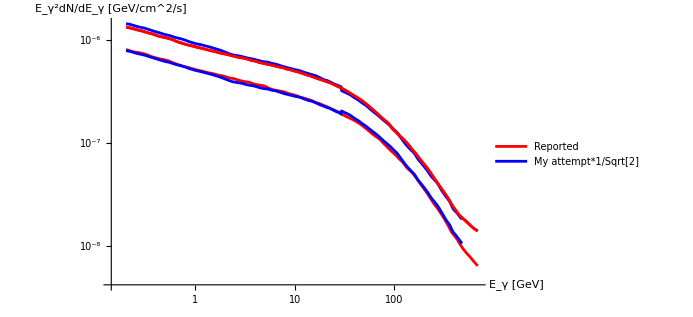

```mathematica
ListLogLogPlot[{knownUpperData,knownLowerData,Transpose[{10^allError[[All,1]],knownMidData[[All,2]]*10^allError[[All,2]]}],Transpose[{10^allError[[All,1]],knownMidData[[All,2]]/10^allError[[All,2]]}],knownUpperData},Joined->True,PlotRange->All,PlotStyle->{Red,Red,Blue,Blue},PlotLegends->Placed[{"Reported",None,"My attempt*1/Sqrt[2]"},{0.5,0.2}],AxesLabel->{"E_γ [GeV]","E_γ^2dN/dE_γ [GeV/cm^2/s]"}]
```

```mathematica
Transpose[{allError[[All,1]],knownMidData[[All,2]]*10^allError[[All,2]]}][[612]]
Transpose[{allError[[All,1]],knownMidData[[All,2]]*10^allError[[All,2]]}][[613]]
SFlogDiff[[612]]
SFlogDiff[[613]]
FSRQlogDiff[[612]]
FSRQlogDiff[[613]]
```

{1.46862,3.72752×10^-7}

{1.47217,3.38379×10^-7}

{1.46862,0.181633}

{1.47217,0.18168}

{1.46862,0.240781}

{1.47217,0}